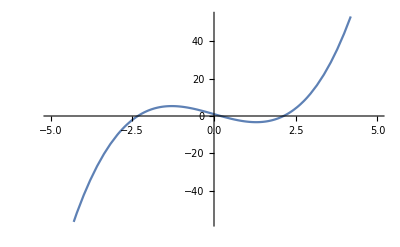

```mathematica
SecantME[x0_,x1_,error_,f_]:=
Module[{xk,xk1,xk2},xk=N[x0];xk1=N[x1];xk2=xk1;
i=0;
Output={};
While[Abs[f[xk2]]>error,
xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);
interval="["<>ToString[NumberForm[xk,12]]<>","<>ToString[NumberForm[xk1,12]]<>"]";
xk=xk1;xk1=xk2;
i++;
Output=Append[Output,{i,interval,xk2,f[xk2]}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"i","Interval","xi","f[xi]"}}],8]];
Print["Number of iterations required to achieve desired accuracy = ",i];
Print["Root after ",i," iterations = ",NumberForm[xk2,8]];
Print["Function value at approximate root, f[xi] = ",NumberForm[f[xk2],8]];];
Question 1
f[x_]:=x^3-5x+1;
error=10^(-4);
Plot[f[x],{x,-5,5}]
```

```mathematica
SecantME[0,1,error,f]
```

i | Interval | xi | f[xi]
1 | [0.,1.] | 0.25 | -0.234375
2 | [1.,0.25] | 0.18644068 | 0.074277312
3 | [0.25,0.186440677966] | 0.20173626 | -0.00047111617
4 | [0.186440677966,0.201736256179] | 0.20163985 | -8.642293×10^-7

Number of iterations required to achieve desired accuracy = 4

Root after 4 iterations = 0.20163985

Function value at approximate root, f[xi] = -8.642293×10^-7

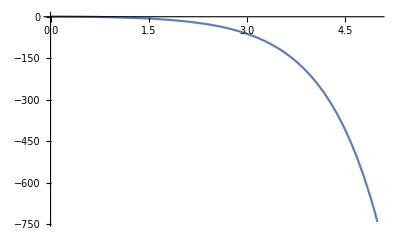

```mathematica
Question 2
f[x_]:=Cos[x]-x*Exp[x];
error=10^(-4);
Plot[f[x],{x,0,5}]
```

```mathematica
SecantME[0,1,error,f]
```

i | Interval | xi | f[xi]
1 | [0.,1.] | 0.31466534 | 0.51987117
2 | [1.,0.314665337801] | 0.44672814 | 0.20354478
3 | [0.314665337801,0.446728144591] | 0.53170586 | -0.042931093
4 | [0.446728144591,0.531705860645] | 0.51690447 | 0.0025927631
5 | [0.531705860645,0.516904467567] | 0.51774747 | 0.000030111941

Number of iterations required to achieve desired accuracy = 5

Root after 5 iterations = 0.51774747

Function value at approximate root, f[xi] = 0.000030111941

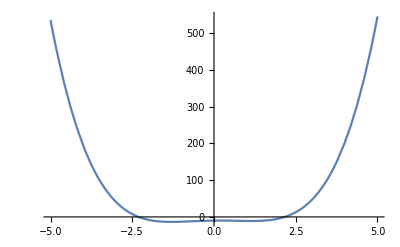

```mathematica
Question 3
f[x_]:=x^4-3*x^2+x-10;
error=10^(-4);
Plot[f[x],{x,-5,5}]
```

```mathematica
SecantME[2,3,error,f]
```

i | Interval | xi | f[xi]
1 | [2.,3.] | 2.0784314 | -2.2198625
2 | [3.,2.07843137255] | 2.119995 | -1.1637008
3 | [2.07843137255,2.11999499205] | 2.1657906 | 0.096032538
4 | [2.11999499205,2.16579064846] | 2.1622995 | -0.0036507762
5 | [2.16579064846,2.16229953415] | 2.1624274 | -0.000010786812

Number of iterations required to achieve desired accuracy = 5

Root after 5 iterations = 2.1624274

Function value at approximate root, f[xi] = -0.000010786812